```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
```

```mathematica
β0 =8.;
```

```mathematica
Ωlist = Table[ReadList[NotebookDirectory[]<>"OmegaGWbeta"<>ToString[NumberForm[β0,{3,2}]]<>"j"<>ToString@index<>".dat",Table[Number,3]],{index,{0}}];
LLΩk = {Interpolation[Log10@{#[[1]],#[[2]]}&/@Mean@Ωlist,InterpolationOrder->1],Interpolation[Log10@{#[[1]],#[[3]]}&/@Mean@Ωlist,InterpolationOrder->1]};
```

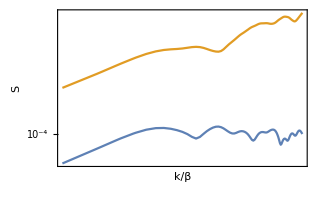

```mathematica
Plot[{LLΩk[[1]][x],LLΩk[[2]][x]},{x,LLΩk[[1,1,1,1]],LLΩk[[1,1,1,2]]},FrameLabel->{"k/β","S"},ImageSize->{320,Automatic},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}}]
```

```mathematica
ρlist = Table[ReadList[NotebookDirectory[]<>"OmegaTotGWbeta"<>ToString[NumberForm[β0,{3,2}]]<>"j"<>ToString@index<>".dat",Table[Number,4]],{index,{0}}];
ρt = Table[{Interpolation[{#[[1]],#[[3]]}&/@ρlist[[j]],InterpolationOrder->1],Interpolation[{#[[1]],#[[4]]}&/@ρlist[[j]],InterpolationOrder->1]},{j,Length@ρlist}];
```

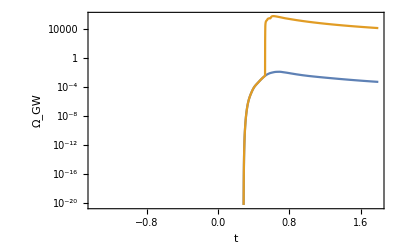

```mathematica
LogPlot[#[t]&/@Flatten[ρt]//Evaluate,{t,ρt[[1,1,1,1,1]],ρt[[1,1,1,1,2]]},FrameLabel->{"t","Ω_GW"}]
```